Preamble

```mathematica
(* Don't share variables with other open notebooks *)
SetOptions[EvaluationNotebook[],CellContext->Notebook]
(* Define color set *)
magenta = RGBColor[{205,16,118}/255];
purple =Lighter[RGBColor[{152,66,227}/255]];
turquoise =Lighter[RGBColor[{53,173,153}/255]];
orange=RGBColor[{0.917647,0.682353,0.105882}];
blue=RGBColor[{0.372549,0.596078,1}];
gray=RGBColor[{.8,.8,.8}];
crimson=RGBColor[{1.0,.3882,.2784}];

(* make a custom ColorFunction *)
purpmap=(Blend[{magenta, purple,turquoise},#]&);

(* Set Plot Options for graphs *)
SetOptions[{ListLinePlot,Plot,ParametricPlot},BaseStyle->{FontFamily->"Open Sans",FontWeight->Bold,FontSize->14},PlotStyle->{{Thick,magenta},{Thick,purple},{Thick,turquoise},{Thick,orange},{Thick,blue},{Thick,gray},{Thick,crimson}}];
SetOptions[{ListPlot,ListLogLogPlot,ListLogPlot},BaseStyle->{FontFamily->"Open Sans",FontWeight->Bold,FontSize->14},PlotStyle->{{magenta},{purple},{turquoise},{orange},{blue},{gray},{crimson}},PlotMarkers->{Automatic,10}];
SetOptions[{DensityPlot,ContourPlot},BaseStyle->{FontFamily->"Open Sans",FontWeight->Bold,FontSize->14}];
SetOptions[StreamPlot,StreamStyle->Thick,StreamScale->Automatic,StreamPoints->Automatic,BaseStyle->{FontFamily->"Open Sans",FontWeight->Bold,FontSize->20}];
(*SetOptions[VectorPlot,VectorColorFunction->purpmap,VectorStyle->Thick,BaseStyle->{FontFamily->"Open Sans",FontSize->20}];*)

(* Turn off the questionable tooltips*)
SetOptions[EvaluationNotebook[],CodeAssistOptions->{"FloatingElementEnable"->False}]

(* Change host directory and import packages*)
SetDirectory[NotebookDirectory[]]
(*<<SuperconductorFunctions`*)
```

/Users/william/Documents/Research/feldman lab/genetic variation

```mathematica
findPSD::usage=
"
Given data set of the form {{t1,f1},t2,f2},...}, find a PSD and express it in terms of natural f frequency bins
Given:
s(t) = Sin[2 π f0 t]
Return:
 P(f)=Delta(f-f0)

The 'peaks' in the signal will occur every 1/f, on average
";
findPSD[data_]:=Module[{tvals,dtVal,fftVals,powspecVals,freqBins},
(*
*)
tvals=Transpose[data][[1]];
dtVal=tvals[[2]]-tvals[[1]];
fftVals=Fourier[Transpose[data][[1]]];
powspecVals=Norm/@fftVals;
powspecVals=Abs@Fourier[Transpose[data][[2]]];
freqBins=(Range[Length[Transpose[data][[2]]]]-1)/(Length[tvals]*(tvals[[2]]-tvals[[1]]));
Transpose[{freqBins,powspecVals}]
]
```

```mathematica
(* Clear everything when something goes wrong *)
ClearAll["Global`*"]
```

```mathematica
texExpression[exp_]:=Module[{outString,texrules,texrules2},
texrules = {"\\text{a1}"->"a_1","\\text{a2}"->"a_2","\alpha"->"\\barc","\\text{a2}"->"a_2","\\text{d1}"->"d_1","\\text{d2}"->"d_2","\\text{a3}"->"a_3","\\text{b2}"->"b_2","\\text{b1}"->"b_1","\\text{k1}"->"k_1","\\text{k2}"->"k_2","\\text{k4}"->"k_4","\\text{k4}"->"k_4"};
texrules2 = {" ^"->"^"};
outString=StringReplace[ToString[TeXForm[exp]],texrules];
Print[StringReplace[outString,texrules2]]
]
```

## My model

#### Define system and plot trajectories

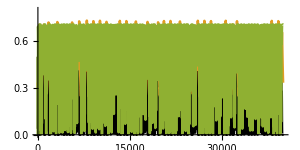

{0.705844,0.333684,0.00366845}

-Graphics3D-

```mathematica
dxt=x((a1 α)/(1+b1 α)(1-k1 x(δ αi-α)-0*10(1/vv) x(δ αi-α)^3)  -d1 (1+k4(.5 ((δ αi)^4-α^4)-.5 ((δ αi)^2-α^2)))-(yMax)(a2  y)/(1+b2 x));
dxt=x((a1 α)/(1+b1 α)(1-k1 x(δ αi-α))  -d1 (1+k4 ((δ αi)^4-α^4)-k2((δ αi)^2-α^2))-a3 y/(1+b2 x));

dyt=y((a2 x)/(1+b2 x) - d2 ) ;

innerDer=D[dxt/x, αi];
dxt0=dxt;
dxt=(dxt)/.{αi->α};
innerDer=(innerDer/.{αi->α});
dαt=vv innerDer;



params={a1->5/2,δ->1,a2->.1/2,d1->.4/2.5,d2->.01/2.5,b1->6,k1->6,k4->9,k2->9,b2->2/1.5,vv->1/1000,a3->.4};(*stable*)

params={a1->5/2,δ->1,a2->.1/2,d1->.4/2.5,d2->.01/2.5,b1->6,k1->6,k4->9,k2->9,b2->2/1.5,vv->1/3*.2,a3->.4};(*cycling*)

params={a1->5/2,δ->1,a2->.1/2,d1->.4/2.5,d2->.01/2.5,b1->6,k1->6,k4->9,k2->9,b2->2/1.5,vv->1/3,a3->.4};(*chaos*)

ic = {α[0]==.5,x[0]==.5,y[0]==.3};


simTime=8*5000;

systemRHS={dxt,dyt,dαt}/.params/.{x->x[t],y->y[t],α->α[t]};
systemLHS={x'[t],y'[t],α'[t]};
system=MapThread[#1==#2&,{systemLHS,systemRHS}];
simOut=NDSolve[Join[system,ic],{x[t],y[t],α[t]},{t,0,simTime},MaxSteps->∞,InterpolationOrder->1(*,Method->"StiffnessSwitching",WorkingPrecision->32*)(*,StartingStepSize->1/500,Method->{"FixedStep",Method->"ExplicitEuler"}*)];

dynPlot=Plot[Evaluate[{x[t],y[t],α[t]}/.simOut[[1]]],{t,0,simTime},PlotStyle->{{Thickness[.006],Black},{Thickness[.006],magenta},{Thickness[.006],turquoise}},(*PlotRange->Automatic,*)AspectRatio->1/2,ImageSize->300,PlotRange->{{0,simTime},{0,.8}}]
Print[{α[t],y[t],x[t]}/.simOut[[1]]/.t->simTime]
ParametricPlot3D[Evaluate[{α[t],y[t],x[t]}/.simOut[[1]]],{t,0,simTime},PlotStyle->{purple},PlotRange->All,BoxRatios->{1, 1, 1}]
(*Export["figure resources/bifurcation dynamics/cycling_tall.EPS",dynPlot,Background->None]*)
```

#### Make kymographs of fitness landscape

```mathematica
(*Find the locations of the maximima in the fitness landscape,  also do not include cases where maxima is greater than zero. The goal is to overlay this on the kymograph showing the potential itself varying*)
zeroLocs[t_]=Evaluate[(αi/.NSolve[D[dxt0/x/.params,αi]==0,αi])]/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]];
peakLocs[tval_?NumericQ]:=Module[{eq1,eq2},
eq1={D[dxt0/x/.params,{αi,2}]<0}/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]/.t->tval;
eq2={D[dxt0/x/.params,αi]==0}/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]/.t->tval;(αi/.NSolve[Flatten[{eq1,eq2}],αi])
];
bottLocs[tval_?NumericQ]:=Module[{eq1,eq2},
eq1={D[dxt0/x/.params,{αi,2}]>0}/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]/.t->tval;
eq2={D[dxt0/x/.params,αi]==0}/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]/.t->tval;(αi/.NSolve[Flatten[{eq1,eq2}],αi])
];


{tStart,tEnd}={400,700};
{tStart,tEnd}={230,530};
{tStart,tEnd}={230,730};
tvals=Array[#&,3000,{tStart,tEnd}];
locVals=zeroLocs/@tvals;
pklocVals=peakLocs/@tvals;
bottlocVals=bottLocs/@tvals;
```

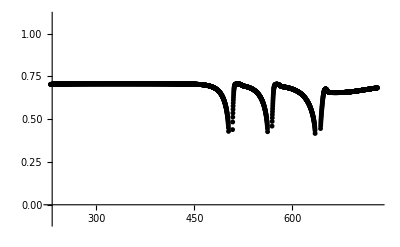

```mathematica
inflPlot=ListPlot[Flatten[MapThread[Table[{#1,Re[#2[[ii]]]},{ii,1,Length[#2]}]&,{tvals,locVals}],1],PlotRange->{{tStart,tEnd},{-.1,1.1}},PlotStyle->blue];
maxLocPlot=ListPlot[Flatten[MapThread[Table[{#1,Re[#2[[ii]]]},{ii,1,Length[#2]}]&,{tvals,pklocVals}],1],PlotRange->{{tStart,tEnd},{-.1,1.1}},PlotStyle->Black,PlotMarkers->{Automatic,5}];
minLocPlot=ListPlot[Flatten[MapThread[Table[{#1,Re[#2[[ii]]]},{ii,1,Length[#2]}]&,{tvals,bottlocVals}],1],PlotRange->{{tStart,tEnd},{-.1,1.1}},PlotStyle->White,PlotMarkers->{Automatic,5}];
maximaPlt=Show[{minLocPlot,maxLocPlot}]
```

```mathematica
fitScape[t_,αi_]=(dxt0/x/.params/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]);


tvals=Array[#&,200,{tStart,tEnd}];
αvals=Array[#&,40,{0,1}];

tαvals=Flatten[Outer[N[{#1,#2}]&,tvals,αvals],1];
fitScapeVals=fitScape@@@tαvals;

tαfitScapeVals=MapThread[{#1[[1]],#1[[2]],#2}&,{tαvals,fitScapeVals}];
transformtαfitScapeVals=MapThread[{#1[[1]],#1[[2]],Sign[#2]*Log[Abs[#2]+1]}&,{tαvals,fitScapeVals}];

Needs["DivergentColorMaps`"]
clrBound=Max[{Abs[Max[#]],Abs[Min[#]]}]&[Transpose[transformtαfitScapeVals][[3]]];
fitKymo2=ListDensityPlot[transformtαfitScapeVals,InterpolationOrder->0,PlotRange->{{tStart,tEnd},{-.05,1.05},{-clrBound,clrBound}},ColorFunction->CoolToWarm,AspectRatio->1/3];

landscapePlot=Show[{fitKymo2,maximaPlt},BaseStyle->{FontFamily->"Open Sans",FontWeight->Bold,FontSize->14}];
(*Export["figure resources/landscape_figure/xxlandscape.PNG",landscapePlot,ImageResolution->300]*)
```

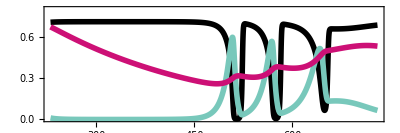

/Users/william/Documents/Research/feldman lab/genetic variation/figure resources/landscape figure/dynamics_boxed.EPS

```mathematica
dynPlot=Plot[Evaluate[{α[t],x[t],y[t]}/.simOut[[1]]],{t,tStart,tEnd},PlotStyle->{{Thickness[.01],Black},{Thickness[.01],turquoise},{Thickness[.01],magenta}},PlotRange->{{tStart,tEnd},{0,.8}},AspectRatio->1/3,Frame->True]
(*Export["/Users/william/Documents/Research/feldman lab/genetic variation/figure resources/landscape figure/dynamics_boxed.EPS",dynPlot,ImageResolution->300]*)
```

```mathematica
(*Cycling while the predator density stays within some range: {400,700}*)
(*Entry into cycling: slow decline of predator abundance causes increase of width of prey trait distribution (even as mean remains relatively fixed), also slow downshift of mean*)
```

(1. δ^2-6. αi^2 δ^4)/vv

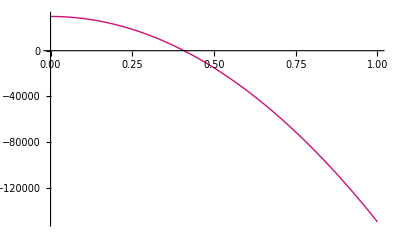

```mathematica
(* Sign change in the inverse susceptibility, or dx/dαi *)
D[dxt0/x,{αi,2}]//FullSimplify
Plot[Evaluate[D[dxt0/x,{αi,2}]/.params],{αi,0,1}]
```

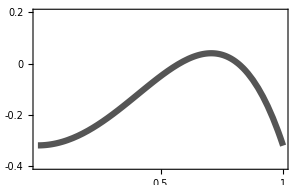

./figure resources/landscape figure/fitnessSnapshot1.PNG

```mathematica
fitSlicePlot=Plot[{fitScape[400,αi]},{αi,0,1},PlotStyle->{Thickness[.015],Darker[Gray]},PlotRange->{{0,1},{-.4,.2}},Frame->True,ImageSize->300,FrameTicks->{{{-.4,-.2,0,.2},None},{{.5,1},None}}]
Export["./figure resources/landscape figure/fitnessSnapshot1.PNG",fitSlicePlot,ImageResolution->300]
(*Show[{eqαPlot,fitSlicePlot},PlotRange->Automatic]*)
```

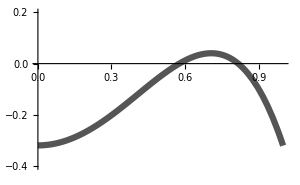

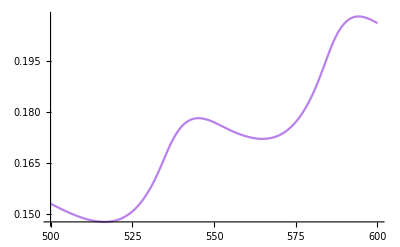

```mathematica
Plot[Evaluate[{y[t](*,α[t],x[t]*)}/.simOut[[1]]],{t,500,600},PlotStyle->{purple},PlotRange->All]
```

#### Study hysteresis effects

This should be done analytically and then compared to the numerical results for entry into a cycle---might need to work in large V limit or something to reduce dimensionality

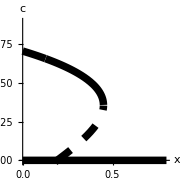

```mathematica
eqs=Solve[{(D[dxt0/x,αi]/.α->αi)==0},αi]/.δ->1;
allEqs=eqs/.params;
hystPlot=Plot[Evaluate[αi/.allEqs],{x,0,.8},PlotRange->{-.01,.9},AspectRatio->1,PlotStyle->{{Thickness[.03],Black},{Thickness[.03],Black},{Thickness[.03],Black},{Thickness[.03],Dashing[.07],Black}},ImageSize->Small,AxesLabel->{"x","c"}]
(*Export["/Users/william/Documents/Research/feldman lab/genetic variation/figure resources/hysteresis/hysteresisPlot.PNG",hystPlot,ImageResolution->600]*)
```

```mathematica
(* Check out the concavities of the solutions*)
Plot[Evaluate[Sign[D[dxt0/x/.params,{αi,2}]/.allEqs]],{x,0,1}];
```

```mathematica
(* Write out the equilibria*)
tt=αi/.eqs;
gg=(-576 b1^2 d1^3 k2 k4^2+128 d1^3 k4^3+432 a1 b1^2 d1^2 k1 k4^2 x+√(4 (-24 b1^2 d1^2 k2 k4-16 d1^2 k4^2)^3+(-576 b1^2 d1^3 k2 k4^2+128 d1^3 k4^3+432 a1 b1^2 d1^2 k1 k4^2 x)^2));
tt[[2]]-(-1/(3 b1)+(-24 b1^2 d1^2 k2 k4-16 d1^2 k4^2)/(6 2^(2/3) b1 d1 k4 (gg)^(1/3))-1/(12 2^(1/3) b1 d1 k4)(gg)^(1/3))
tt[[4]]-((-1/(3 b1)-((1-ⅈ √3) (-24 b1^2 d1^2 k2 k4-16 d1^2 k4^2))/(12 2^(2/3) b1 d1 k4 (gg)^(1/3))+1/(24 2^(1/3) b1 d1 k4)(1+ⅈ √3) (gg)^(1/3)))
```

0

0

```mathematica
(*Find maximum value of cbar observed in the dynamics*)
αi /. eqs[[3]] /. x -> 0
αi /. eqs[[3]] /. x -> 0/.params
```

-1/(3 b1)-((1+ⅈ √3) (-24 b1^2 d1^2 k2 k4-16 d1^2 k4^2))/(12 2^(2/3) b1 d1 k4 (-576 b1^2 d1^3 k2 k4^2+128 d1^3 k4^3+√(4 (-24 b1^2 d1^2 k2 k4-16 d1^2 k4^2)^3+(-576 b1^2 d1^3 k2 k4^2+128 d1^3 k4^3)^2))^(1/3))+1/(24 2^(1/3) b1 d1 k4)(1-ⅈ √3) (-576 b1^2 d1^3 k2 k4^2+128 d1^3 k4^3+√(4 (-24 b1^2 d1^2 k2 k4-16 d1^2 k4^2)^3+(-576 b1^2 d1^3 k2 k4^2+128 d1^3 k4^3)^2))^(1/3)

0.707107+1.11022×10^-16 ⅈ

0.707107+1.11022×10^-16 ⅈ

```mathematica
(*Look for first critical values of x*)
αi /. {eqs[[2]],eqs[[4]]}; (*Inspect these two solutions for any square or quartic roots*)
turnpts=Solve[√(4 (-24 b1^2 d1^2 k2 k4-16 d1^2 k4^2)^3+(-576 b1^2 d1^3 k2 k4^2+128 d1^3 k4^3+432 a1 b1^2 d1^2 k1 k4^2 x)^2)==0,x]//FullSimplify
turnpts/.params
eqs/.turnpts/.params
```

{{x→-(2 (2 a1 d1 k1 k4 (-9 b1^2 k2+2 k4)+√2 √(a1^2 d1^2 k1^2 k4 (3 b1^2 k2+2 k4)^3)))/(27 a1^2 b1^2 k1^2 k4)},{x→(2 (2 a1 d1 k1 (9 b1^2 k2-2 k4) k4+√2 √(a1^2 d1^2 k1^2 k4 (3 b1^2 k2+2 k4)^3)))/(27 a1^2 b1^2 k1^2 k4)}}

{{x→-0.195074},{x→0.449494}}

{{{αi→0},{αi→-0.467567+5.96028×10^-9 ⅈ},{αi→0.768466-8.32667×10^-17 ⅈ},{αi→-0.467567-5.96028×10^-9 ⅈ}},{{αi→0},{αi→-0.879578},{αi→0.356455-7.29982×10^-9 ⅈ},{αi→0.356455+7.29982×10^-9 ⅈ}}}

```mathematica
(*Look for second critical value of x*)
```

```mathematica
xcrit2=Solve[(αi /. eqs[[4]])==0,x]
xcrit2/.params
ccrit2=eqs[[3]]/.xcrit2//FullSimplify;
eqs/.xcrit2/.params
ccrit2/.params
```

{{x→(2 d1 k2)/(a1 k1)}}

{{x→0.192}}

{{{αi→0},{αi→-0.795334+5.55112×10^-17 ⅈ},{αi→0.628667+1.11022×10^-16 ⅈ},{αi→5.55112×10^-17-1.11022×10^-16 ⅈ}}}

```mathematica
dxt0/x/.δ->1
```

-(a3 y)/(1+b2 x)+(a1 α (1-k1 x (-α+αi)))/(1+b1 α)-d1 (1-k2 (-α^2+αi^2)+k4 (-α^4+αi^4))

The concavity of the phase diagram suggests that the origin is stable whenever x > x**
Or equivalently, that the fitness peak at the origin is highest when x > .2, making that the true critical point
the overlap region x** < x < x is the “two phase” region where the other local maximum is metastable

```mathematica
(*Find the latent heat*)
x0=(2 d1 k2)/(a1 k1);
ent=D[-dxt0/x/.δ->1,x]/.{x->x0,α->αi}//FullSimplify
(*ContourPlot[x*ent/.params,{x,0,1},{y,0,1}]*)
```

-(a1^2 a3 b2 k1^2 y)/(a1 k1+2 b2 d1 k2)^2

#### Study the 1D and 2D cases

The fixed - trait system undergoes a bifurcation, in which an unstable limit cycle suddenly appears at α=0.104, and a stable point at the origin simultaneously loses stability

α < αc, stable points at origin and negative interior

```mathematica
(*Look for cycles without evolution*)
RealPosQ[thing_]:=AllTrue[Re[#]>=0&&Abs@Im[#]<10^(-12)&/@thing,#&];
(*params={a1->5/2,δ->1,a2->.1/2,d1->.5/2.5,d2->.01/2.5,b1->6,k1->6,k4->9,k2->9,b2->2/1.5,vv->1/3,yMax->8};*)
αval=.103896;
αval=.105;
systemRHS0={dxt,dyt}/.α->αval/.params/.{x->x[t],y->y[t]};
eqVals0={x[t],y[t]}/.NSolve[systemRHS0==0,{x[t],y[t]}];
solMap={x->#[[1]],y->#[[2]]}&/@Select[eqVals0,RealPosQ];
solMap={x->#[[1]],y->#[[2]]}&/@eqVals0
jacob0=D[{dxt/.α->αval,dyt/.α->αval}/.params,{{x,y}}]/.solMap⟦1⟧;
Eigenvalues[jacob0]
```

{{x→0.0895522,y→0.00291869},{x→0.,y→0.}}

{0.0000556237+0.00192969 ⅈ,0.0000556237-0.00192969 ⅈ}

Solve the 1D case

```mathematica
(* Solve 1D case*)
Clear[flat]
flat=(dxt/.y->0/.δ->1)/.x->xx[t];
Solve[(dxt/.y->0/.δ->1)==0,x]//FullSimplify
DSolve[xx'[t]==flat,xx[t],t]//FullSimplify
```

{{x→0}}

{{xx[t]→ⅇ^(-(t (d1-a1 α+b1 d1 α))/(1+b1 α)) C[1]}}

```mathematica
Reduce[ {d1-a1 α+b1 d1 α>0,d1>0,a1>0,b1>0,α>0,b1 d1 <a1},α]
```

d1>0&&a1>0&&0<b1<a1/d1&&0<α<-d1/(-a1+b1 d1)

```mathematica
{b1 d1, a1}/.params//N
```

{0.96,2.5}

Study the 2D case

```mathematica
(* Solve the Jacobian *)
sols2D=Solve[({dxt,dyt}/.δ->1)==0,{x,y}]//FullSimplify
jacob2D=D[{dxt,dyt}/.δ->1(*/.params*),{{x,y}}]/.sols2D;
eigs2D=Eigenvalues/@jacob2D
```

{{x→d2/(a2-b2 d2),y→-(a2 (d1-a1 α+b1 d1 α))/(a3 (a2-b2 d2) (1+b1 α))},{x→0,y→0}}

{{1/(2 a2 a3 (1+b1 α))(-a3 b2 d1 d2+a1 a3 b2 d2 α-a3 b1 b2 d1 d2 α-a3 √d2 √(d1-a1 α+b1 d1 α) √(4 a2^2-4 a2 b2 d2+b2^2 d1 d2+4 a2^2 b1 α-4 a2 b1 b2 d2 α-a1 b2^2 d2 α+b1 b2^2 d1 d2 α)),1/(2 a2 a3 (1+b1 α))(-a3 b2 d1 d2+a1 a3 b2 d2 α-a3 b1 b2 d1 d2 α+a3 √d2 √(d1-a1 α+b1 d1 α) √(4 a2^2-4 a2 b2 d2+b2^2 d1 d2+4 a2^2 b1 α-4 a2 b1 b2 d2 α-a1 b2^2 d2 α+b1 b2^2 d1 d2 α))},{-d2,(-d1+a1 α-b1 d1 α)/(1+b1 α)}}

```mathematica
(*Existence of interior solution*)
intCo=Reduce[{-(a2 (d1-a1 α+b1 d1 α))/(a3 (a2-b2 d2) (1+b1 α))>0,d2/(a2-b2 d2)>0,d1>0,a1>0,a2>0,a3>0,b1>0,d1>0,α>0,b2>0},α]

(*Stability of Interior solution*)
stabCo=Reduce[{(d1-a1 α+b1 d1 α)>0,d1>0,a1>0,b1>0,d1>0,α>0,intCo},α]

(* Imaginary eigenvalues *)
pp= (d1-a1 α+b1 d1 α )(4 a2^2 (1+b1 α)-4 a2 b2 d2 (1+b1 α)+b2^2 d2 (d1-a1 α+b1 d1 α))<0;
imagCo=Reduce[{pp,(d1-a1 α+b1 d1 α)<0,d1>0,a1>0,a2>0,a3>0,b1>0,d1>0,α>0,b2>0,intCo},α]
```

d2>0&&a2>0&&0<b2<a2/d2&&d1>0&&a1>0&&0<b1<a1/d1&&a3>0&&α>-d1/(-a1+b1 d1)

False

(a3>0&&d2>0&&a2>0&&0<b2<a2/d2&&d1>0&&a1>0&&0<b1<(a1 b2^2 d2)/(4 a2^2-4 a2 b2 d2+b2^2 d1 d2)&&-d1/(-a1+b1 d1)<α<(-4 a2^2+4 a2 b2 d2-b2^2 d1 d2)/(4 a2^2 b1-4 a2 b1 b2 d2-a1 b2^2 d2+b1 b2^2 d1 d2))||(a3>0&&d2>0&&a2>0&&0<b2<a2/d2&&d1>0&&a1>0&&(a1 b2^2 d2)/(4 a2^2-4 a2 b2 d2+b2^2 d1 d2)≤b1<a1/d1&&α>-d1/(-a1+b1 d1))

```mathematica
(*Stability of mutual exclusion solution*)
Reduce[{-d1+a1 α-b1 d1 α<0,α>0,d1>0,a1>0,b1>0},α]
```

d1>0&&a1>0&&((0<b1<a1/d1&&0<α<-d1/(-a1+b1 d1))||(b1≥a1/d1&&α>0))

stable and unstable points annihilate at critical value, produce an unstable interior limit cycle and an unstable point at origin

```mathematica
simTime=8000;

params={a1->5/2,δ->1,a2->.1/2,d1->.4/2.5,d2->.01/2.5*3,b1->6,k1->6,k4->9,k2->9,b2->2/1.5,vv->1/3,a3->.4};(*chaos*)
ic = {α[0]==.5,x[0]==.5,y[0]==.3};

systemRHS0={dxt,dyt}/.α->.2/.params/.{x->x[t],y->y[t]};

systemLHS={x'[t],y'[t]};
system=MapThread[#1==#2&,{systemLHS,systemRHS0}];
simOut=NDSolve[Join[system,ic],{x[t],y[t]},{t,0,simTime},MaxSteps->∞,InterpolationOrder->1(*,Method->"StiffnessSwitching",WorkingPrecision->32*)(*,StartingStepSize->1/500,Method->{"FixedStep",Method->"ExplicitEuler"}*)];
dynPlot=Plot[Evaluate[{x[t],y[t]}/.simOut[[1]]],{t,0,simTime},PlotStyle->{{Thickness[.004],Black},{Thickness[.004],magenta},{Thickness[.004],turquoise}},(*PlotRange->Automatic,*)AspectRatio->1/3,ImageSize->500(*,PlotRange->{{0,simTime},{0,.9}}*)]
Print[{y[t],x[t]}/.simOut[[1]]/.t->simTime]
```

-Graphics-

{9.35322×10^84,5.93476×10^226}

```mathematica
(*Look for stability without the predator*)
RealPosQ[thing_]:=AllTrue[Re[#]>0&&Abs@Im[#]<10^(-12)&/@thing,#&];
params={a1->.5*5/2,δ->1,d1->.4/2.5,d2->.01/2.5,b1->6,k1->6,k2->9,k4->9,a2->.1/2,b2->2/1.5,yMax->8,vv->1/3};

systemRHS0={dxt,dαt}/.y->0/.params/.{x->x[t],α->α[t]};
eqVals0={x[t],α[t]}/.NSolve[systemRHS0==0,{x[t],α[t]}];
solMap={x->#[[1]],α->#[[2]]}&/@Select[eqVals0,RealPosQ]
jacob0=D[{dxt/.y->0,dαt/.y->0}/.params,{{x,α}}]/.solMap;
Eigenvalues[jacob0]
```

{{x→0.304959,α→0.103896}}

{0.159616+0.259032 ⅈ,0.159616-0.259032 ⅈ}

#### Study distribution of prey epoch lengths

```mathematica
origSign=D[dxt0/x,αi]/.αi->0/.params;
tvals=Array[#&,100000,{0,.1simTime}];
```

```mathematica
sysValsRules=({x->#[[1]],y->#[[2]],α->#[[3]]})&/@sysVals;
```

```mathematica
Solve[(D[dxt0/x,αi]/.δ->1)==0,αi](*/.params/.sysValsRules[[150]]*);
rootLoc=(2^(1/3) (1-ⅈ √3) d1 k2)/(((432 a1 d1^2 k1 k4^2 x α)/(1+b1 α)+√(-55296 d1^6 k2^3 k4^3+(186624 a1^2 d1^4 k1^2 k4^4 x^2 α^2)/(1+b1 α)^2))^(1/3))+((1+ⅈ √3) ((432 a1 d1^2 k1 k4^2 x α)/(1+b1 α)+√(-55296 d1^6 k2^3 k4^3+(186624 a1^2 d1^4 k1^2 k4^4 x^2 α^2)/(1+b1 α)^2))^(1/3))/(24 2^(1/3) d1 k4)/.params;
```

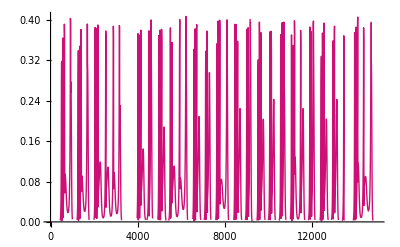

```mathematica
ff[t_]=rootLoc/.{x->x[t],y->y[t],α->α[t]}/.simOut;
Plot[ff[t],{t,0,simTime}]
```

```mathematica
sysVals=Transpose[{x[t],y[t],α[t]}/.simOut[[1]]/.t->tvals];
```

```mathematica
rootLocVals=(rootLoc/.{x->#[[1]],y->#[[2]],α->#[[3]]})&/@sysVals;
```

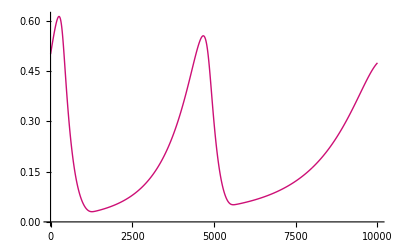

```mathematica
ListLinePlot[Transpose[sysVals][[1]][[1;;10000]]]
```

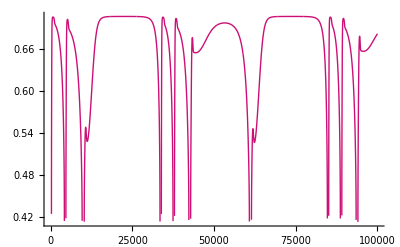

```mathematica
ListLinePlot[rootLocVals,PlotRange->All]
```

```mathematica
(*Study distribution of prey epochs*)
```

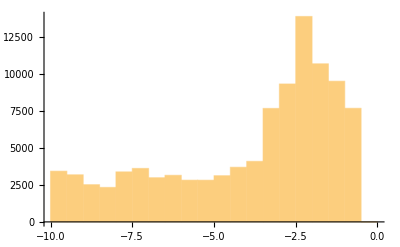

```mathematica
tvals=Array[#&,100000,{0,simTime}];
Histogram[Log[x[t]]/.simOut[[1]]/.t->tvals]
```

```mathematica
simTime=20*5000;
simOut=NDSolve[Join[system,ic],{x[t],y[t],α[t]},{t,0,simTime},MaxSteps->∞,InterpolationOrder->1(*,Method->"StiffnessSwitching",WorkingPrecision->32*)(*,StartingStepSize->1/500,Method->{"FixedStep",Method->"ExplicitEuler"}*)];
```

```mathematica
1/simTime NIntegrate[x[t]/.simOut[[1]],{t,0,simTime}]
1/simTime NIntegrate[Log[x[t]]/.simOut[[1]],{t,0,simTime}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2112.03}. NIntegrate obtained 4773.81 and 492.697 for the integral and error estimates.

0.0954761

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {6932.82}. NIntegrate obtained -192722. and 1725.26 for the integral and error estimates.

-3.85445

{{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48},{1,3,2,1,0,1,174,82,93,42,19,9,3,1,1,1,2,2,4,9,4,28,29}}

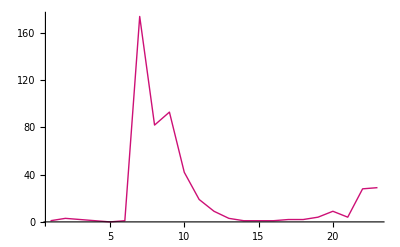

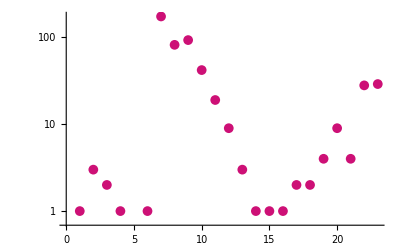

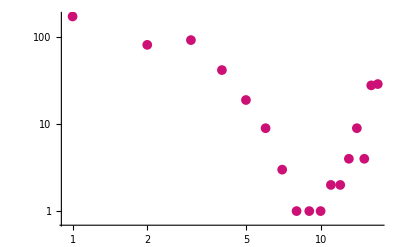

```mathematica
threshVal = 0.1353;
threshVal = 0.3;
tvals=Array[#&,100000,{0,simTime}];
xvals=x[t]/.simOut[[1]]/.t->tvals;
dtVal=tvals[[2]]-tvals[[1]];

binArray=#>threshVal&/@xvals;
runLengths=If[#[[1]],Length[#]*dtVal,##&[]]&/@Split[binArray];
kk=HistogramList[runLengths,Ceiling@Sqrt[Length[runLengths]]]
ListLinePlot[kk[[2]][[;;]],PlotRange->All]
ListLogPlot[kk[[2]][[;;]]]
ListLogLogPlot[kk[[2]][[7;;]]]
```

#### Find Global Lyapunov spectrum

```mathematica
(*Find global spectrum*)
```

```mathematica
<<lceFork.m
F[{x_,y_,α_}]={dxt,dyt,dαt}/.params
```

ReplaceAll::reps: {params} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{dxt,dyt,dαt}/.params

```mathematica
(*Single run*)
Kval=20
Tval=50;
dtStep=.02;
transientSkip=5;
(*Total time*)Kval*Tval
(*kk=*)LCEsC[F,{.5,.5,.2},Tval,Kval,transientSkip,dtStep]//AbsoluteTiming
```

20

1000

{98.2879,{{0.00345142,0.00266421,-0.719957},2.00849}}

```mathematica
(* Many short runs *)
nPts=9;
icRangeSimTime=40000;
icTvals=RandomReal[{0,icRangeSimTime},nPts]
icSim=NDSolve[Join[system,ic],{x[t],y[t],α[t]},{t,0,icRangeSimTime},MaxSteps->∞,InterpolationOrder->1];
icList=Transpose[{x[t],y[t],α[t]}/.icSim[[1]]/.t->icTvals];

Kval=20
Tval=50;
dtStep=.02;
transientSkip=5;
(*Total time*)Kval*Tval
allOuts=LCEsC[F,#,Tval,Kval,transientSkip,dtStep]&/@icList
(*allOuts=ParallelTable[LCEsC[F,icList[[ii]],Tval,Kval,transientSkip,dtStep],{ii,1,Length[icList]}]*)
```

{25808.2,9951.32,4373.14,29647.,19741.8,23847.9,6449.4,27090.6,14057.4}

20

1000

```mathematica
allAllOuts=Import["resources/shortRuns.mx"];
```

Last::nolast: {} has zero length and no last element.

```mathematica
allAllOuts={{{0.000044281225891575016,-0.0005616221167798616,-0.739085862502026},1.078845231639857},{{0.0038120372848028266,0.0010260168833853638,-0.7231731190807975},2.00669003595479},{{0.002687818360699166,-0.0028985267806116858,Indeterminate},1.9273049946193517},{{0.0020263581731506464,0.00013495985149185487,-0.7128130595962662},2.0030320965582007},{{0.006351235403196902,-0.00026896542199016284,-0.7415237782361543},2.0082023937191527},{{0.007998924774475035,0.001456092495470991,Indeterminate},Indeterminate},{{0.008306454506968415,-0.00029115422903372255,-0.7238078246958278},2.011073796116121},{{0.0002977693840748581,-0.0009546111304456355,-0.7001046420293763},1.3119274169114834},{{0.00994076056675809,-0.0024502592890929963,-0.7086708523694101},2.0105697888556033},{{0.006957658399201615,0.0005986148491491243,-0.7206255844746687},2.0104857132624},{{0.0044615437366068164,-0.0007830121803686509,-0.6929846210475701},2.0053082441435386},{{0.01038926507108725,-0.0003762345678825225,-0.7109305966461447},2.0140843994483313},{{0.004920320110816641,-0.002754969905408731,-0.7003700210600428},2.0030917231467598},{{0.0006865290470781293,-0.0017678656638350821,-0.7309421025161946},1.3883377912260721},{{0.0013693899783081905,0.0011184932625038434,-0.7056259693103399},2.0035257818575523},{{0.0013146312877718898,0.0003141806877631614,Indeterminate},Indeterminate},{{0.00912894997584447,0.00013684276370252247,-0.7099768078072365},2.0130508386156505},{{0.0017831197623502742,-0.000010334788992381938,-0.7052827657668195},2.002513580452275},{{0.007158202811972485,0.0001817509838190865,-0.7214061968204452},2.010174508935662},{{0.0013460611577883993,0.00003143315215270159,-0.7114242275232677},2.0019362488043693},{{0.007448146403422363,-0.0004852894753538599,-0.7005162045920161},2.0099396086520565},{{0.004459218154383756,0.002484155782063672,-0.7240390941823645},2.0095897776684124},{{0.0012039696608100755,-0.0061374905580294774,-0.7088858175346913},1.196166437964611},{{0.0040699999480475115,-0.0005087206363389605,-0.7100460054560906},2.005015561364113},{{0.0033200791538818375,-0.0024485592194246762,-0.7296599285905964},2.001194419345654},{{0.004817762178962415,-0.0002290533136641144,-0.7085508195253407},2.006476188776935},{{0.0037934958869839295,0.0011375017393042632,Indeterminate},Indeterminate},{{0.012508126268289664,-0.0015198333150790494,-0.7140697068349339},2.015388263705956},{{0.0001301278317378547,-0.002076844865465561,-0.7359893492779915},1.0626565006860462},{{0.002566783208452673,0.0011153887903420463,Indeterminate},Indeterminate},{{0.0008271445137713305,0.00006880409068142224,-0.7151209645268823},2.0012528630104494},{{0.004015441494553619,-0.0011815507604315137,-0.710605584937119},2.0039879938944933},{{0.005638105899742252,-0.0015587801028550362,-0.7157289065255152},2.0056995403702365},{{0.0010963456665618314,-0.0006232028831540859,-0.7081060311270374},2.0006681806997952},{{0.0004278950833880826,-4.192351194002963*^-6,-0.7226853482440424},2.0005862893626163},{{0.005089332948258098,-0.00008237246037693136,-0.7061513098246093},2.007090492389124},{{0.0036070696052767897,0.0008438331312421852,Indeterminate},Indeterminate},{{0.004660650784042917,0.0016061313923036197,-0.7155943287362678},2.008757450869424},{{0.0051735450426948345,0.0009763938303034088,-0.7070644801983479},2.0086978472900703},{{0.009762236145500655,-0.0030750946018643,-0.719142862116207},2.0092987664842537},{{0.002837669816098313,-0.0009895555554482694,Indeterminate},Indeterminate},{{0.005959526804620825,-0.001614588486995491,-0.7139078699368876},2.0060861331000726},{{0.010251651889217787,0.0013026947093897092,-0.726612250851994},2.0159016677534125},{{0.0015664331975690368,-0.0018875322828577749,-0.7226645999537361},1.8298841888931374},{{0.002107597478948635,0.00009480606723968265,-0.7175458608395464},2.0030693557950587},{{0.005910527098958694,-0.0016261730055480528,-0.7191432327072528},2.0059575810472166},{{0.00692693376675028,-0.00039591204779979727,Indeterminate},Indeterminate},{{0.0032077708013404766,-0.0002851537142653013,-0.7250233961170598},2.0040310658976352},{{0.002141232325463064,-0.000024417825330045328,-0.7365742151349346},2.002873864515805},{{0.001139644444435431,-0.0027399918914884818,-0.7378403325962982},1.4159298602217127},{{0.0008889537082384842,0.0005717978359545664,-0.6967689301078763},2.0020964648121824},{{0.007966382540265094,0.000160507627407112,-0.7168230486967125},2.0113373728459876},{{0.0026738357090869305,-0.0023786692224627795,-0.7109981970447963},2.0004151437905904},{{0.00621731822158373,-0.0037843689469456198,Indeterminate},Indeterminate},{{0.007043761133276541,-0.0007794380144988806,-0.7077765464398912},2.008850707402339},{{0.0020668044574455994,-0.000837287026715337,Indeterminate},Indeterminate},{{0.002752584452983468,-0.0004865086650203865,-0.68740423323815},2.0032965694396268},{{0.0061364064648272406,-0.0006962633319796643,-0.7298283294936694},2.0074540037882906}};
```

```mathematica
Median[Cases[Transpose[Transpose[allAllOuts][[1]]][[1]],_?NumericQ]]
MedianDeviation[Cases[Transpose[Transpose[allAllOuts][[1]]][[1]],_?NumericQ]]

Median[Cases[Transpose[Transpose[allAllOuts][[1]]][[2]],_?NumericQ]]
MedianDeviation[Cases[Transpose[Transpose[allAllOuts][[1]]][[2]],_?NumericQ]]

Median[Cases[Transpose[Transpose[allAllOuts][[1]]][[3]],_?NumericQ]]
MedianDeviation[Cases[Transpose[Transpose[allAllOuts][[1]]][[3]],_?NumericQ]]

Median[Cases[Transpose[allAllOuts][[-1]],_?NumericQ]]
MedianDeviation[Cases[Transpose[allAllOuts][[-1]],_?NumericQ]]
```

0.00350219

0.00164474

-0.000283044

0.000988929

-0.713817

0.00684243

2.00485

0.00275359

```mathematica
(* Few Long Runs *)
nPts=5;
icRangeSimTime=40000;
icTvals=RandomReal[{0,icRangeSimTime},nPts]
icSim=NDSolve[Join[system,ic],{x[t],y[t],α[t]},{t,0,icRangeSimTime},MaxSteps->∞,InterpolationOrder->1];
icList=Transpose[{x[t],y[t],α[t]}/.icSim[[1]]/.t->icTvals];

Kval=50
Tval=100;
dtStep=.02;
transientSkip=5;
(*Total time*)Kval*Tval
allOuts=LCEsC[F,#,Tval,Kval,transientSkip,dtStep]&/@icList
(*allOuts=ParallelTable[LCEsC[F,icList[[ii]],Tval,Kval,transientSkip,dtStep],{ii,1,Length[icList]}]*)
```

{1428.95,22616.7,23921.6,3584.81,12808.}

50

5000

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{0.00330194,0.0000776286,-0.342876},2.00986},{{0.00301631,-0.0000443411,Indeterminate},Indeterminate},{{0.0044901,-0.000376754,-0.348098},2.01182},{{0.00365199,0.00031072,-0.346562},2.01143},{{0.00254142,-0.000100544,-0.34704},2.00703}}

```mathematica
allOutsLong=Import["resources/longRuns.mx"];
```

```mathematica
allOutsLong={{{0.0005671731537493223,0.000490586912295885,Indeterminate},Indeterminate},{{0.0031051577225491294,-0.00013491290543313572,-0.3428772370247423},2.008662706346125},{{0.0031944048599558397,-0.0005231943979567483,-0.3474296047898207},2.0076884940867807},{{0.00259187833936029,-0.0006797242501450374,-0.34160046476720146},2.0055976331604772},{{0.002555208147970599,-0.0001348997055025029,Indeterminate},Indeterminate},{{0.002954130723219446,-0.00015955311679327446,-0.3461983096443154},2.008072187323206},{{0.003063516714586323,-0.00048153670105666966,Indeterminate},Indeterminate},{{0.004140562461222856,-0.0003359512703357813,Indeterminate},Indeterminate},{{0.0025444904100870116,-0.000037275144672865327,-0.3486136330233272},2.007191959888862},{{0.0031891810558462145,-0.0009915309554312359,-0.3400920997754276},2.006461926348381},{{0.003301942149849207,0.0000776286263738835,-0.34287632653068995},2.0098565299343307},{{0.0030163100370087315,-0.00004434107660478546,Indeterminate},Indeterminate},{{0.004490102948103691,-0.000376753879518117,-0.34809753602576654},2.0118166566633815},{{0.0036519873388817887,0.000310719740655241,-0.34656207234793923},2.011434335709877},{{0.002541422524368933,-0.00010054386216013276,-0.34703985257560027},2.007033424674698}}
```

{{{0.000567173,0.000490587,Indeterminate},Indeterminate},{{0.00310516,-0.000134913,-0.342877},2.00866},{{0.0031944,-0.000523194,-0.34743},2.00769},{{0.00259188,-0.000679724,-0.3416},2.0056},{{0.00255521,-0.0001349,Indeterminate},Indeterminate},{{0.00295413,-0.000159553,-0.346198},2.00807},{{0.00306352,-0.000481537,Indeterminate},Indeterminate},{{0.00414056,-0.000335951,Indeterminate},Indeterminate},{{0.00254449,-0.0000372751,-0.348614},2.00719},{{0.00318918,-0.000991531,-0.340092},2.00646},{{0.00330194,0.0000776286,-0.342876},2.00986},{{0.00301631,-0.0000443411,Indeterminate},Indeterminate},{{0.0044901,-0.000376754,-0.348098},2.01182},{{0.00365199,0.00031072,-0.346562},2.01143},{{0.00254142,-0.000100544,-0.34704},2.00703}}

```mathematica
Median[Cases[Transpose[Transpose[allOutsLong][[1]]][[1]],_?NumericQ]]
MedianDeviation[Cases[Transpose[Transpose[allOutsLong][[1]]][[1]],_?NumericQ]]

Median[Cases[Transpose[Transpose[allOutsLong][[1]]][[2]],_?NumericQ]]
MedianDeviation[Cases[Transpose[Transpose[allOutsLong][[1]]][[2]],_?NumericQ]]

Median[Cases[Transpose[Transpose[allOutsLong][[1]]][[3]],_?NumericQ]]
MedianDeviation[Cases[Transpose[Transpose[allOutsLong][[1]]][[3]],_?NumericQ]]

Median[Cases[Transpose[allOutsLong][[-1]],_?NumericQ]]
MedianDeviation[Cases[Transpose[allOutsLong][[-1]],_?NumericQ]]
```

0.00310473

0.000642525

-0.000121042

0.000248136

-0.345916

0.00230183

2.00864

0.00201981

```mathematica
Total[{0.004293821028820805,0.003849558507971454,-0.3442373151585195}]
```

-0.336094

```mathematica
2+(0.004293821028820805+0.003849558507971454)/0.3442373151585195
```

2.02366

#### Find Local Lyapunov spectrum

Initialize the relevant functions

```mathematica
eigs[t_]=Eigenvalues[D[{dxt,dyt,dαt},{{x,y,α}}]/.params]/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]];
maxReEgs[t_]=Max[Re/@eigs[t]];
maxReEigsC=Compile[{{t,_Real}},maxReEgs[t],RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];

(*Faster*)
valmap[tval_]=Evaluate[{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]/.t->tval];
eigSys=Eigenvalues[D[{dxt,dyt,dαt},{{x,y,α}}]/.params];
eigs2[t_]:=eigSys/.valmap[t]
maxReEgs2[t_]=Max@Re@eigs2[t];
```

Plot the eigenvalues over a short interval in order to illustrate switching

```mathematica
tvals=Array[#&,1600,{230,730}];
allEigsVals=eigs2/@tvals;
```

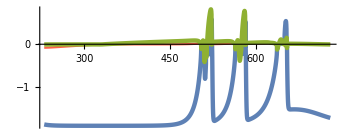

```mathematica
timeUnits=1;
pltEigsVals=Transpose[{tvals,#}]&/@Re[Transpose[allEigsVals]];
eigValsPlot=ListLinePlot[pltEigsVals,AspectRatio->1/2.5,PlotStyle->{Thickness[.009],{orange,blue,crimson}},ImageSize->350]
(*Export["./figure resources/lyapunov/eigplot.png",eigValsPlot,ImageResolution->300]*)
```

Get a distribution of epoch lengths

```mathematica
tvals=Array[#&,200000,{0,simTime}];
(*maxEigsVals=maxReEgs2/@tvals;*)
(*Export["./resources/maxEigsVals_simTime20000.mx",maxEigsVals]*)
maxEigsVals=Import["./resources/maxEigsVals_simTime20000.mx"];
```

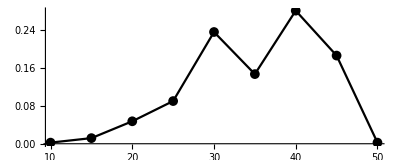

```mathematica
threshVal=0.0;
threshVal=0.2;
dtVal=tvals[[2]]-tvals[[1]];
binArray=(#>threshVal)&/@maxEigsVals;
runLengths=If[#[[1]],Length[#]*dtVal,##&[]]&/@Split[binArray];
kk=HistogramList[runLengths,-20+Ceiling@Sqrt[Length[runLengths]]];

histYvals=kk[[2]]/Total[kk[[2]]];
histXvals=kk[[1]][[2;;]];
epochPlot=ListLinePlot[Transpose[{histXvals,histYvals}],AspectRatio->1/2.5,PlotRange->All,PlotMarkers->{{●, 10}},PlotStyle->Black]
(*Export["./figure resources/lyapunov/test_simTime200000_thresholdp2.png",epochPlot,ImageResolution->300]*)
```

```mathematica
(*Plot the relationship between x values and hte max eigenvalues*)
ListPlot[Transpose[{xVals,maxEigsVals}],PlotMarkers->{Automatic,5},PlotStyle->Black,PlotRange->All]
```

#### Plot strange attractor

```mathematica
tvals=Array[#&,200000,{0,.3simTime}];
sysvals = Evaluate[{α[t],x[t],y[t]}/.simOut[[1]]]/.t->tvals;
vp=Options[Graphics3D,ViewPoint][[1,2]];
attractorLinePlot=ListPointPlot3D[Transpose[sysvals],PlotStyle->{Black,Thickness[.008]},PlotRange->All,Axes->False,BoxRatios->{1, 1, 1},Axes->False,ViewPoint->Dynamic[vp],Boxed->False,AxesLabel->{"α","x","y"}(*,ColorFunction->cfn*)(*Boxed->{Back,Bottom,Left}*)]/.Point->Line
imAttract=Image[attractorLinePlot,ImageResolution->600];
(*Export["figure resources/strange_attractor.PNG",imAttract,ImageResolution->600,Background->None]*)
```

figure resources/strange_attractor.PNG

```mathematica
(*2D projections of the attractor*)
```

```mathematica
tvals=Array[#&,80000,{0,simTime}];
sysvals = Evaluate[{α[t],x[t],y[t]}/.simOut[[1]]]/.t->tvals;
Image@ListPlot[Transpose[{sysvals[[2]],sysvals[[1]]}],PlotStyle->{Black,Thickness[.001]},PlotRange->All,AspectRatio->1,AxesLabel->{"x","α"},PlotMarkers->{Automatic,2}]
Image@ListPlot[Transpose[{sysvals[[1]],sysvals[[3]]}],PlotStyle->{Black,Thickness[.001]},PlotRange->All,AspectRatio->1,AxesLabel->{"α","y"},PlotMarkers->{Automatic,2}]
Image@ListPlot[Transpose[{sysvals[[2]],sysvals[[3]]}],PlotStyle->{Black,Thickness[.001]},PlotRange->All,AspectRatio->1,AxesLabel->{"x","y"},PlotMarkers->{Automatic,2}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Image@ListPlot[Transpose[{sysvals[[2]],sysvals[[3]]}],PlotStyle->{Black,Thickness[.001]},PlotRange->{{0,.6},{.25,.735}},AspectRatio->1,AxesLabel->{"x","y"},PlotMarkers->{Automatic,2}]
```

-Graphics-

#### Find power spectrum and characteristic frequency

The peak gives f in Sin[2 π f t]; Peaks on average occur every 1/f

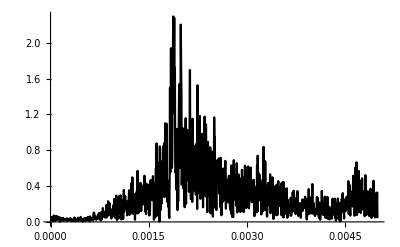

```mathematica
tvals=Array[#&,40000,{0,simTime}];
(*dtVal=N[tvals[[2]]-tvals[[1]]];*)
xVals=Evaluate[x[t]/.simOut[[1]]]/.t->tvals;
kk=findPSD[Transpose[{tvals,xVals}]];
psdPlot=ListLinePlot[kk[[2;;1000]],PlotRange->All,PlotStyle->Black]
(*Export["figure resources/landscape_figure/PSD.PNG",psdPlot,ImageResolution->600]*)
```

#### Make Poincare map

0.107276

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

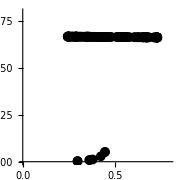

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

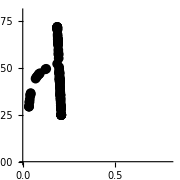

0.443739

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

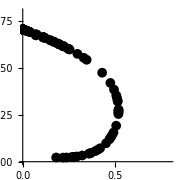

```mathematica
SetDirectory[NotebookDirectory[]];
Get["RootSearch.m"];
(*medVal=1/simTime Integrate[Evaluate[x[t]/.simOut[[1]]],{t,0,simTime}]
tvals=RootSearch[Evaluate[x[t]/.simOut[[1]]]==.5,{t,0,simTime}];
tvals = t/.tvals;*)

medVal=1/simTime Integrate[Evaluate[x[t]/.simOut[[1]]],{t,0,simTime}]
tvals=RootSearch[Evaluate[x[t]/.simOut[[1]]]==medVal,{t,0,simTime}];
tvals = t/.tvals;

f[t_]=Evaluate[{x[t],y[t],α[t]}/.simOut[[1]]];
poincareVals=f/@tvals;

rr1=ListPlot[{#[[2]],#[[3]]}&/@poincareVals,AspectRatio->1,PlotRange->{{0,.8},{0,.8}},ImageSize->Small,PlotStyle->Black]


medVal=1/simTime Integrate[Evaluate[α[t]/.simOut[[1]]],{t,0,simTime}];
tvals=RootSearch[Evaluate[α[t]/.simOut[[1]]]==medVal,{t,0,simTime}];
tvals = t/.tvals;

f[t_]=Evaluate[{x[t],y[t],α[t]}/.simOut[[1]]];
poincareVals=f/@tvals;

rr2=ListPlot[{#[[1]],#[[2]]}&/@poincareVals,AspectRatio->1,PlotRange->{{0,.8},{0,.8}},ImageSize->Small,PlotStyle->Black]


medVal=1/simTime Integrate[Evaluate[y[t]/.simOut[[1]]],{t,0,simTime}]
tvals=RootSearch[Evaluate[y[t]/.simOut[[1]]]==medVal,{t,0,simTime}];
tvals = t/.tvals;

f[t_]=Evaluate[{x[t],y[t],α[t]}/.simOut[[1]]];
poincareVals=f/@tvals;

rr3=ListPlot[{#[[1]],#[[3]]}&/@poincareVals,AspectRatio->1,PlotRange->{{0,.8},{0,.8}},ImageSize->Small,PlotStyle->Black]
```

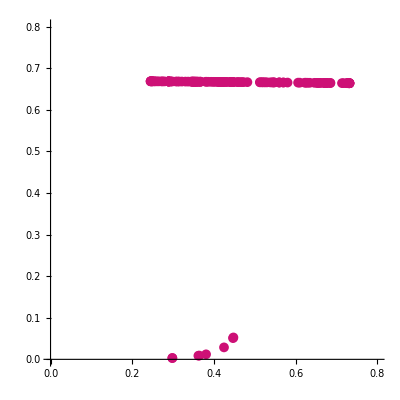

```mathematica
rr1
```

```mathematica
Export["ycplane.PNG",rr1,ImageResolution->600]
Export["xyplane.PNG",rr2,ImageResolution->600]
Export["xcplane.PNG",rr3,ImageResolution->600]
```

ycplane.PNG

xyplane.PNG

xcplane.PNG

#### Mean versus distributional dynamics

This is probably a particle-based simulation: defined a bunch of individuals with their own trait values ci, but with a mean that agrees with some initial condition
Each timestep: update the x and y differential equations using the average of the distribution

x_i(t) = x(t; c_i)

Try numerically solving with a particle-like simulation

```mathematica
nSampVals=50;
αiVals=Table[α[ii]->RandomVariate[NormalDistribution[ic[[1]][[2]],1]],{ii,1,nSampVals}];
xiVals=Table[x[ii,0]==(ic[[2]][[2]])/nSampVals,{ii,1,nSampVals}];
```

```mathematica
(*inner=dxt0/.{α->β}/.{x->x[n,t],y->y[t],αi->α[n]}/.β -> (∑_(n=1)^nSampVals x[n,t]α[n])/(∑_(n=1)^nSampVals x[n,t])/.params;
Table[∂_t x[n,t]==inner,{n,1,nSampVals}]/.αiVals*)
```

```mathematica
(*lhsx=dxt0/.{x->x[n,t],y->y[t]}/.α -> (∑_(n=1)^nSampVals x[n,t]α[n])/(∑_(n=1)^nSampVals x[n,t])/.αiVals/.params;*)
simTime2=200;
lhsy=dyt/.{x->∑_(n=1)^nSampVals x[n,t],y->y[t]}/.params;
icVals =Flatten@Join[{ic[[3]], xiVals}];
(*allODE0 = Table[∂_t x[n,t]==lhsx,{n,1,nSampVals}];*)
inner=dxt0/.{α->β}/.{x->x[n,t],y->y[t],αi->α[n]}/.β -> (∑_(n=1)^nSampVals x[n,t]α[n])/(∑_(n=1)^nSampVals x[n,t])/.params;
allODE0=Table[D[x[n,t], t]==inner,{n,1,nSampVals}]/.αiVals;
allODE=Flatten@Join[{icVals,allODE0,y'[t]==lhsy}];
allDepVars=Flatten@Join[{y[t],Table[x[ii,t],{ii,1,nSampVals}]}];
outVals=NDSolve[allODE,allDepVars,{t,0,simTime2}];
```

$Aborted

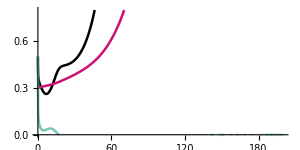

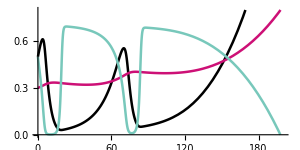

```mathematica
Plot[Evaluate[{∑_(n=1)^nSampVals x[n,t],y[t],((∑_(n=1)^nSampVals x[n,t]α[n])/(∑_(n=1)^nSampVals x[n,t]))/.αiVals}/.outVals],{t,0,simTime2},PlotStyle->{{Thickness[.006],Black},{Thickness[.006],magenta},{Thickness[.006],turquoise}},AspectRatio->1/2,PlotRange->{{0,simTime2},{0,.8}}]
Plot[Evaluate[{x[t],y[t],α[t]}/.simOut[[1]]],{t,0,simTime2},PlotStyle->{{Thickness[.006],Black},{Thickness[.006],magenta},{Thickness[.006],turquoise}},AspectRatio->1/2,PlotRange->{{0,simTime2},{0,.8}}]
(*Plot[Evaluate[((∑_(n=1)^nSampVals x[n,t]α[n])/(∑_(n=1)^nSampVals x[n,t]))/.αiVals/.outVals],{t,0,5}]*)
```

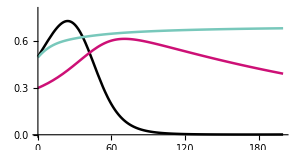

Try just solving for equilibrium points

```mathematica
numSols=NSolve[Join[Table[0==inner,{n,1,nSampVals}]/.αiVals,{lhsy==0}],allDepVars,Reals,Method->{"UseSlicingHyperplanes"->False},WorkingPrecision->5,VerifySolutions->False];
numSolPts={∑_(n=1)^nSampVals x[n,t],y[t],((∑_(n=1)^nSampVals x[n,t]α[n])/(∑_(n=1)^nSampVals x[n,t]))/.αiVals}/.numSols
```

$Aborted

{5.75316×10^-22,-1.15587×10^-33,1.5352}

```mathematica
initGuesses=MapThread[{#1,#2}&,{allDepVars,ConstantArray[10,nSampVals+1]}];
rootSyst=Join[Table[0==inner,{n,1,nSampVals}]/.αiVals,{lhsy==0}];
numSols=FindRoot[rootSyst,initGuesses];
numSolPts={∑_(n=1)^nSampVals x[n,t],y[t],((∑_(n=1)^nSampVals x[n,t]α[n])/(∑_(n=1)^nSampVals x[n,t]))/.αiVals}/.numSols
```

{-0.0721248,-6.85481×10^-26,-0.0238653}

{{0.0895522,-1.74325,-0.0877154},{0.0895522,-0.447761,0},{0,0,0},{0.304959,0,0.103896},{0,0,-0.707107},{0,0,0.707107},{0,0,-0.707107},{0.0895522,0.487,0.673605}}

-Graphics3D-

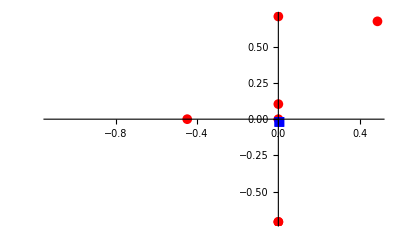

```mathematica
solPts={x,y,α}/.NSolve[{dxt==0,dyt==0,dαt==0}/.params,{x,y,α},Reals]
ListPointPlot3D[{solPts,.0005+{numSolPts}},PlotStyle->{{Red,PointSize[.03]},{Blue,PointSize[.03]}}]

solPts={y,α}/.NSolve[{dxt==0,dyt==0,dαt==0}/.params,{x,y,α},Reals];
ListPlot[{solPts,.005+{numSolPts[[2;;]]}},PlotStyle->{{Red,PointSize[.03]},{Blue,PointSize[.03]}}]
```

#### Try solving full integro-PDE

```mathematica
pdeSyst={D[x[α,t], t]==((dxt0/.δ->1/.α->(∫_(-∞)^∞ px[α,t] αⅆα)/(∫_(-∞)^∞ px[α,t] ⅆα)/.αi->α)/.{x->x[α,t],y->y[α,t]}/.{px[α,t]->x[α,t]}),D[y[α,t], t]==(dyt/.{x->x[α,t],y->y[α,t]})}/.params;
initConditions={x[α,0]==ic[[2]][[2]]*PDF[NormalDistribution[ic[[1]][[2]],1],α],y[α,0]==ic[[3]][[2]]};
allPDEparts=Join[pdeSyst,initConditions];

simTime2=200;
simBox=5;
ufun[α_,t_] = NDSolveValue[allPDEparts,{x[α,t],y[α,t]},{α,-simBox,simBox},{t,0,simTime2},AccuracyGoal->10,PrecisionGoal->10,MaxSteps->Infinity,MaxStepSize->.01(*,Method -> {"PDEDiscretization" -> {"MethodOfLines", 
"SpatialDiscretization" -> {"TensorProductGrid", 
"MinPoints" -> 1000}}}*)];
```

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
subregions=Max@Dimensions@InterpolatingFunctionGrid[Head@(ufun[α,t][[1]])];

meanα[t_?NumericQ]:=NIntegrate[ufun[α,t][[1]]α,{α,-simBox,simBox}(*,Method->{"InterpolationPointsSubdivision","MaxSubregions"->subregions}*)]
totx[t_?NumericQ]:=NIntegrate[ufun[α,t][[1]],{α,-simBox,simBox}(*,Method->{"InterpolationPointsSubdivision","MaxSubregions"->subregions}*)]
(*toty[t_]:=NIntegrate[ufun[α,t][[2]],{α,-simBox,simBox}]*)
toty[t_]:=ufun[0,t][[2]]

tPts=Array[#&,100,{0,simTime2}];
meanαPts=meanα/@tPts;
totxPts=totx/@tPts;
totyPts=toty/@tPts;
```

$Aborted

$Aborted

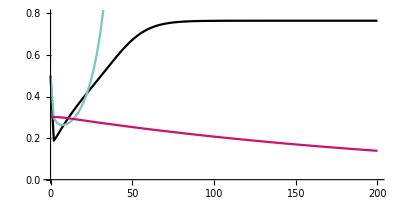

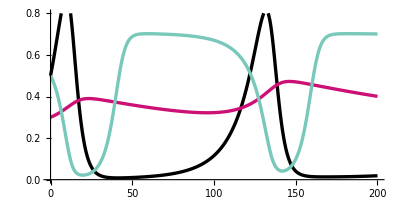

```mathematica
mnaPlt=ListLinePlot[Transpose[{tPts,meanαPts/totxPts}],PlotRange->{0,1},PlotStyle->Black];
xPlt=ListLinePlot[Transpose[{tPts,totxPts}],PlotStyle->turquoise];
yPlt=ListLinePlot[Transpose[{tPts,totyPts}],PlotStyle->magenta];
Show[{mnaPlt,xPlt,yPlt},AspectRatio->1/2,PlotRange->{{0,simTime2},{0,.8}}]

Plot[Evaluate[{x[t],y[t],α[t]}/.simOut[[1]]],{t,0,simTime2},PlotStyle->{{Thickness[.006],Black},{Thickness[.006],magenta},{Thickness[.006],turquoise}},AspectRatio->1/2,PlotRange->{{0,simTime2},{0,.8}}]
```

```mathematica
ContourPlot[ufun[α,t][[1]],{α,-simBox,simBox},{t,0,simTime2},ColorFunction->"TemperatureMap",AspectRatio->1];
ContourPlot[ufun[α,t][[2]],{α,-simBox,simBox},{t,0,simTime2},ColorFunction->"TemperatureMap",AspectRatio->1];
```

#### Try generating velocity time series

Try finding the vector field along a mean-field solution
+ Given x,y, and mean α values at some point on the attractor, make distribution x(α) that agrees with these points
+ plug this distribution into the velocity equation to get ensemble of dot x(α) and dot y(α), and compare the averages to the analytic velocity field

```mathematica
(*tPval = 100;
popVar=10;*)

findDist[tPval_,popVar_]:=Module[{vel,velFromAve,velFromDist,xdist,attractorPoint,uv1,uv2},
attractorPoint={x[t],y[t],α[t]}/.simOut[[1]]/.t->tPval;
xdist[αi_]=attractorPoint⟦1⟧*PDF[NormalDistribution[attractorPoint⟦3⟧,popVar],αi];
;
vel=({dxt0/.x->xdist[αi],dyt/.x->attractorPoint⟦1⟧}/.params/.{y->attractorPoint⟦2⟧,α->attractorPoint⟦3⟧});
velFromDist=NIntegrate[vel*xdist[αi],{αi,-Infinity,Infinity}]/(attractorPoint⟦1⟧);
;
velFromAve={dxt,dyt}/.params/.{x->attractorPoint⟦1⟧,y->attractorPoint⟦2⟧,α->attractorPoint⟦3⟧};
;
uv1=Normalize[velFromDist];
uv2=Normalize[velFromAve];
uv1.uv2
]

(* tPval is the timepoint
popStd is the standard deviation *)
findDist[tPval_,popStd_]:=Module[{vel,velFromAve,velFromDist,xdist,attractorPoint,uv1,uv2},
attractorPoint={x[t],y[t],α[t]}/.simOut[[1]]/.t->tPval;
xdist[αi_]=attractorPoint⟦1⟧*PDF[NormalDistribution[attractorPoint⟦3⟧,popStd],αi];
;
vel=((dxt0/.x->xdist[αi])/.params/.{y->attractorPoint⟦2⟧,α->attractorPoint⟦3⟧});
velFromDist=NIntegrate[vel*xdist[αi],{αi,-Infinity,Infinity}]/(attractorPoint⟦1⟧);
;
velFromAve=(dxt)/.params/.{x->attractorPoint⟦1⟧,y->attractorPoint⟦2⟧,α->attractorPoint⟦3⟧};
;
{velFromDist,velFromAve}
]

findDist[30,1]
(*ListLinePlot[{{{0,0},Normalize[velFromDist]},{{0,0},Normalize[velFromAve]}},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->200]*)
```

{-0.0346026,0.00283104}

```mathematica
stdSampVals=Exp[Array[#1&,20,{Log[.01],Log[10]}]];
allCoors=Table[
tSampVals=N[Array[#1&,1000,{0,.2simTime}]];(findDist[#1,stdSampVals⟦ii⟧]&)/@tSampVals,
{ii,1,Length[stdSampVals]}
];
```

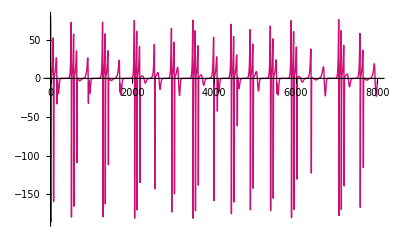

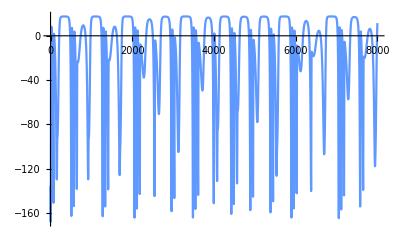

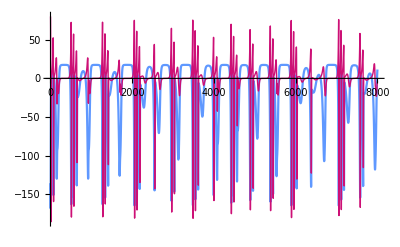

```mathematica
ListLinePlot[{1988 corrVals⟦1;;All,2⟧},PlotRange->All]
ListLinePlot[{corrVals⟦1;;All,1⟧-Median[corrVals⟦1;;All,1⟧]},PlotRange->All,PlotStyle->blue]
Show[{%,%%},PlotRange->All]
```

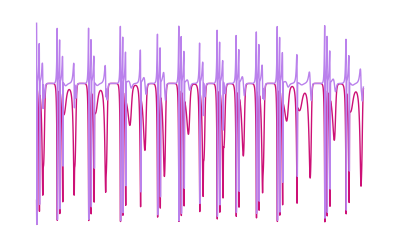

```mathematica
ListLinePlot[{corrVals⟦1;;All,1⟧,1988*corrVals⟦1;;All,2⟧},Axes->{None},PlotRange->All]
```

0.00212098

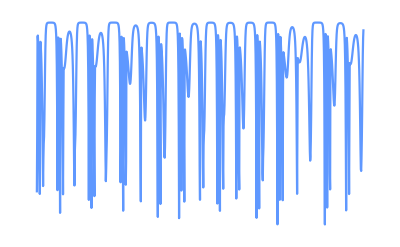

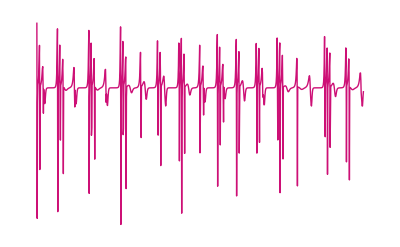

```mathematica
Mean[(Normalize[corrVals[[;;,1]]]-Normalize[corrVals[[;;,2]]])^2]
rr1=ListLinePlot[corrVals[[;;,1]],PlotStyle->blue,Axes->{None},PlotRange->All]
rr2=ListLinePlot[corrVals[[;;,2]],Axes->{None},PlotRange->All]
(*Show[{rr1,rr2}]*)
```

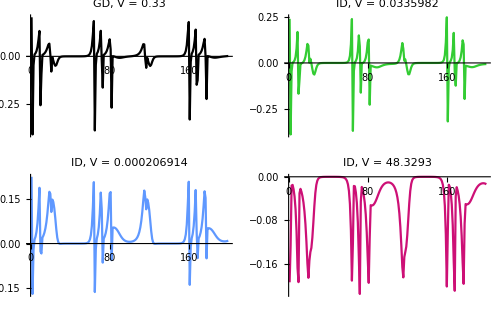

figure resources/Variance_Samples.PNG

```mathematica
loPlt=ListLinePlot[Normalize[allCoors⟦2⟧⟦1;;200,1⟧],PlotStyle->blue,PlotRange->All,PlotLabel->"ID, V = "<>ToString[stdSampVals⟦2⟧^2]];
midPlt=ListLinePlot[Normalize[allCoors⟦9⟧⟦1;;200,1⟧],PlotStyle->RGBColor[{51/255,204/255,51/255}],PlotRange->All,PlotLabel->"ID, V = "<>ToString[stdSampVals⟦9⟧^2]];
hiPlt=ListLinePlot[Normalize[allCoors⟦-2⟧⟦1;;200,1⟧],PlotStyle->magenta,PlotRange->All,PlotLabel->"ID, V = "<>ToString[stdSampVals⟦-2⟧^2]];
origPlt=ListLinePlot[Normalize[allCoors⟦1⟧⟦1;;200,2⟧],PlotStyle->Black,PlotRange->All,PlotLabel->"GD, V = 0.33"];
allPlts=GraphicsGrid[{{origPlt, midPlt},{loPlt,hiPlt}},ImageSize->500];
Export["figure resources/Variance_Samples.PNG",allPlts,ImageResolution->600]
```

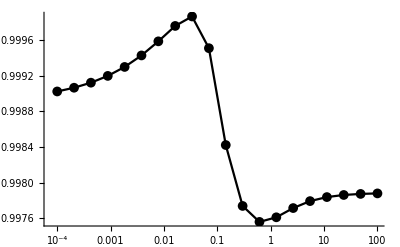

figure resources/MSE_vs_Variance.PNG

```mathematica
coorsScores=1-Mean[(Normalize[#⟦1;;All,1⟧]-Normalize[#⟦1;;All,2⟧])^2]&/@allCoors;


mseVarPlt=ListLogLinearPlot[Transpose[{stdSampVals^2,coorsScores}],Joined->True,PlotMarkers->{Automatic,10},PlotStyle->Black,BaseStyle->{FontFamily->"Open Sans",FontWeight->Bold,FontSize->12}]
(*Export["figure resources/MSE_vs_Variance.PNG",mseVarPlt,ImageResolution->600]*)
```

Lande paper stuff

```mathematica
(* First term in Lande's integral has the fitness averaged already *)
(* Second term averages the fitness after *)

fitnessTerm = dxt0/x;
fitnessTerm = f[x,α,αi];
fitnessTerm = αi-α;

lande=(D[fitnessTerm/.{αi->α},α]/.δ->1)-(D[fitnessTerm,α]/.αi->α/.δ->1)//FullSimplify

(* My update equation*)
me=D[fitnessTerm,αi]/.{αi->α}/.δ->1

me - lande //FullSimplify
```

1

1

0

```mathematica
Plot[dαt/.params/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]],{t,0,simTime}]
```

$Aborted

```mathematica
dαt/.params/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]/.t->100

(dαt-vv*a1)/.params/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]/.t->100
```

-0.00095974

-0.834293

Plot the mean fitness as a function of time

```mathematica
vv*.25/1^2/.params
```

0.0833333

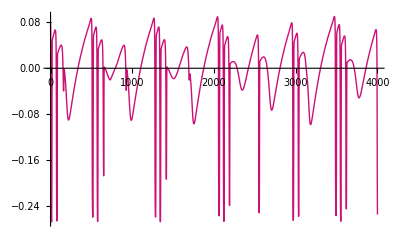

```mathematica
Plot[(dxt0/x/.αi->α/.params/.{x->x[t],y->y[t],α->α[t]}/.simOut[[1]]),{t,0,.1simTime}]
```

#### Plot stabilizing and disruptive landscapes for Figure 1

```mathematica
{αVals,xVals,yVals}={α[t],x[t],y[t]}/.simOut[[1]]/.t->N@Array[#&,10000,{0,simTime}];
Max[αVals]
Min[xVals]
Max[xVals]
Min[yVals]
Max[yVals]
```

0.707091

0.0000460024

0.61201

0.244764

0.732094

```mathematica
fitVals1=dxt0/x/.params/.αi->.2/.(({α->#1⟦1⟧,x->#1⟦2⟧,y->#1⟦3⟧}&)/@Transpose[{αVals,xVals,yVals}]);
fitVals2=dxt0/x/.params/.αi->Sqrt[2]/2/.(({α->#1⟦1⟧,x->#1⟦2⟧,y->#1⟦3⟧}&)/@Transpose[{αVals,xVals,yVals}]);
maxFit=Max[fitVals1];
minFit=Min[fitVals1];
clrScale=Max[{Abs[maxFit],Abs[minFit]}]
```

0.392888

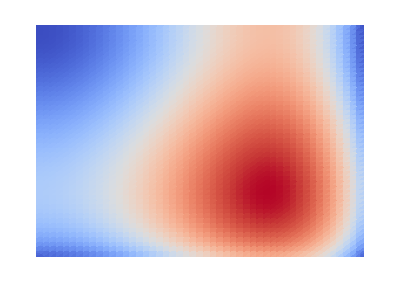

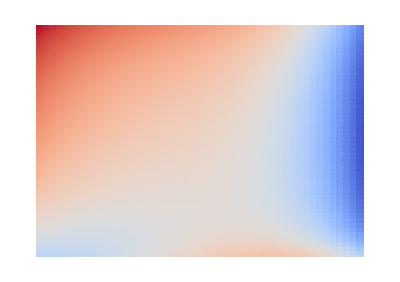

figure resources/lowPrey.PNG

figure resources/hiPrey.PNG

```mathematica
Needs["DivergentColorMaps`"]
{{αmin,αmax},{αimin,αimax}}={{0,Sqrt[2]/2},{0,1}};
fitPlt1=DensityPlot[dxt0/x/.params/.x->.0004/.y->.732,{αi,αimin,αimax},{α,αmin,αmax},ColorFunction->CoolToWarm,PlotRange->{-1,1},AspectRatio->((αmax-αmin)/(αimax-αimin)),Frame->False,PerformanceGoal->"Quality",PlotPoints->50]
fitPlt2=DensityPlot[dxt0/x/.params/.x->.612/.y->.245,{αi,αimin,αimax},{α,αmin,αmax},ColorFunction->CoolToWarm,PlotRange->{-1,1},AspectRatio->((αmax-αmin)/(αimax-αimin)),Frame->False,PerformanceGoal->"Quality",PlotPoints->50]
Export["figure resources/lowPrey.PNG",fitPlt1,ImageResolution->600]
Export["figure resources/hiPrey.PNG",fitPlt2,ImageResolution->600]
```